```mathematica
sample[center_,num_Integer]:=RandomVariate[
MultinormalDistribution[center,IdentityMatrix[3]],
num];
```

```mathematica
clusters={sample[{-1,-1,-1},10000],sample[{1,1,1},10000],sample[{1,-1,1},10000]};
```

```mathematica
Graphics3D[{AbsolutePointSize[.5],
MapThread[{#1,Point[#2]}&,{{Red,Green,Blue},clusters}]},
Background->Black,
PlotRange->6,
Axes->True];
```

```mathematica
net=NetChain[{
DotPlusLayer[400],
ElementwiseLayer[Ramp],
DotPlusLayer[3],
SoftmaxLayer[]
},
"Input"->{3},
"Output"->NetDecoder[{"Class",{Red,Green,Blue}}]
]
```

NetChain[]

```mathematica
NetGraph[net]
```

NetGraph[]

```mathematica
data=RandomSample[
Join@@MapThread[
Thread[#1->#2]&,
{clusters,{Red,Green,Blue}}
]];
```

```mathematica
Length[data]
```

30000

```mathematica
MapThread[f,{{1,2,3},{a,b,c}}]
```

{f[1,a],f[2,b],f[3,c]}

```mathematica
data[[1;;10]]//Column
```

{1.98731,1.24015,0.218188}→RGBColor[0, 0, 1]
{-1.61668,-2.4812,-0.647133}→RGBColor[1, 0, 0]
{1.20363,2.66622,1.88654}→RGBColor[0, 0, 1]
{-0.959034,0.679867,-1.86915}→RGBColor[1, 0, 0]
{-0.218919,-1.4186,-0.0470982}→RGBColor[1, 0, 0]
{-0.0101344,1.79512,0.31952}→RGBColor[0, 0, 1]
{1.21206,-0.853368,-0.553068}→RGBColor[1, 0, 0]
{-0.561037,-1.21897,-0.255397}→RGBColor[1, 0, 0]
{1.58287,0.672328,2.11951}→RGBColor[0, 0, 1]
{3.41491,1.55553,1.95561}→RGBColor[0, 0, 1]

```mathematica
Length[data]
```

20000

```mathematica
training=data[[1;;28000]];
validation=data[[28001;;30000]];
```

```mathematica
result=NetTrain[net,training,MaxTrainingRounds->10000,ValidationSet->validation]
```

NetChain[]

```mathematica
cm=ClassifierMeasurements[result,validation]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.838

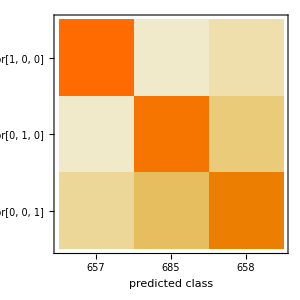

```mathematica
cm["ConfusionMatrixPlot"]
```